```mathematica
G = Exp[(-(DxIn-Dcent)^2)/(2 σ^2)]/(σ√(2 π))
```

(ⅇ^(-(-Dcent+DxIn)^2/(2 σ^2)))/(√(2 π) σ)

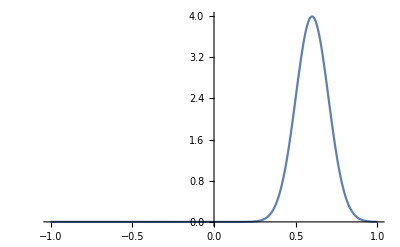

```mathematica
Plot[G/.σ->0.1/.Dcent->0.6,{DxIn,-1,1},PlotRange->Full]
```

```mathematica
Integrate[G,{DxIn,-∞,∞}, Assumptions->σ>0]
```

1

```mathematica
Int=Integrate[G,{DxIn,-Dcrit,Dcrit}, Assumptions->{σ>0, Dcrit>0}]
```

1/2 (-Erf[(Dcent-Dcrit)/(√2 σ)]+Erf[(Dcent+Dcrit)/(√2 σ)])

```mathematica
Simplify[Int-1/2 (Erf[(Dcrit-Dcent)/(√2 σ)]+Erf[(Dcrit+Dcent)/(√2 σ)])]
```

0

```mathematica
DxOut=n1/n2 DxIn
```

(DxIn n1)/n2

```mathematica
DxEff=Simplify[n1/n2 1/Int Integrate[DxIn G,{DxIn,-Dcrit,Dcrit}, Assumptions->{σ>0,Dcrit>0}]]
```

(n1 (Dcent+(ⅇ^(-(Dcent+Dcrit)^2/(2 σ^2)) (-1+ⅇ^((2 Dcent Dcrit)/σ^2)) √(2/π) σ)/(Erf[(Dcent-Dcrit)/(√2 σ)]-Erf[(Dcent+Dcrit)/(√2 σ)])))/n2

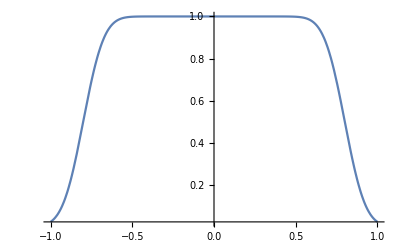

```mathematica
Plot[Int/.σ->0.1/.Dcrit->0.8,{Dcent,-1,1}, PlotRange->All]
```

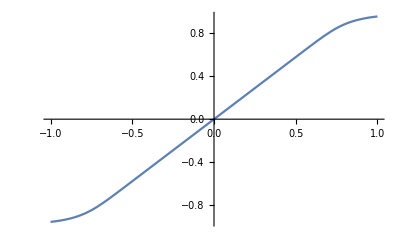

```mathematica
Plot[DxEff/.σ->0.0892/.Dcrit->1.3/1.5/.n1->1.5/.n2->1.3,{Dcent,-1,1}, PlotRange->All]
```

General::munfl: Exp[-847.373] is too small to represent as a normalized machine number; precision may be lost.

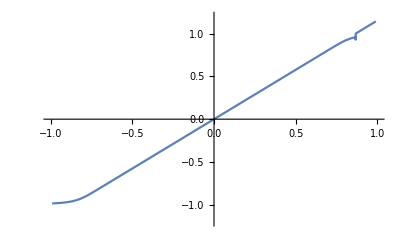

```mathematica
Plot[DxEff/.σ->0.045/.Dcrit->1.3/1.5/.n1->1.5/.n2->1.3,{Dcent,-0.99,0.99}, PlotRange->{{-1,1},{-1.2,1.2}}]
```

```mathematica
Simplify[-2Int-(Erf[(Dcent-Dcrit)/(√2 σ)]-Erf[(Dcent+Dcrit)/(√2 σ)])]
```

0